# Solving Listener Crossword 4151

## Setup

The letters that will be mapped to the first 10 primes

```mathematica
letters={z,i,a,f,t,d,b,l,e,s};
```

Rule sets for mapping a digit to its first letter in its German and English representation

```mathematica
english={0->"Z",1->"O",2->"T",3->"T",4->"F",5->"F",6->"S",7->"S",8->"E",9->"N"};
```

```mathematica
german = {0->"N",1->"E",2->"Z",3->"D",4->"V",5->"F",6->"S",7->"S",8->"A",9->"N"};
```

Each clue index and its expression. 24 has been added to the index of each ' Down' clue, so as to differentiate them from ' Across' clues.

```mathematica
clues={{1,-f-t-a z+(i+z)^2},{4,(f+2 i+t)^2-z},{8,d^2 i-(-d+a d+i) (b+l)+z},{10,b+i z},{11,a+b+e+i+l+s+t},{12,(f+t)^2 (f+t-z)^2},{13,f (d+i)-(a (s+t))/z+z^3},{14,(a+z) (a+b+i+z)},{16,-(-d-f+d i) (b+e+s) z^2+(-d+i)^2 (a-2 z) (a+b+2 d+e+f+2 i+l+s+t+3 z)},{18,-b+i-l+a z},{20,b+d+i+l},{21,a b i},{23,(f+2 i)^2},{24,d^2},{25,(a+d) i+b (a-2 z)},{26,b (a+d)+z+i (-a+d+i) z},{27,a+b},{29,a-2 z+(-d-(d+i) z+a (f+t) z)^2},{30,a+d+i^2-(f+t) (-a+d-z)+z},{31,b-d+(a+i) (2 d+f+2 i+t)-z},{33,a-b+d-f-t+z+(-a+i+(d+i) z)^2},{36,((f+t) (a+d-z)-(a+a^2-i) z)^2},{37,l+(a+b+e+l+s+2 t)^2},{39,b d^2},{41,2 (-d+i) (-b+2 i-z)},{43,a^2},{46,a+b+l+z}};
```

The initial pattern set. When all patterns have been filled, the solution is complete

```mathematica
patterns1={{1,{".",".","."}},{4,{".",".",".","."}},{8,{".",".",".","."}},{10,{".","."}},{11,{".","."}},{12,{".",".",".",".","."}},{13,{".",".","."}},{14,{".",".","."}},{16,{".",".",".",".","."}},{18,{".","."}},{20,{".","."}},{21,{"T",".",".","."}},{23,{".",".",".","."}},{24,{".",".","."}},{25,{".",".","."}},{26,{".",".",".","."}},{27,{".","."}},{29,{".",".",".",".","."}},{30,{".",".","."}},{31,{".",".",".","."}},{33,{".",".",".",".","T"}},{36,{".",".",".",".","."}},{37,{".",".",".","."}},{39,{".",".",".","."}},{41,{".",".","."}},{43,{".",".","."}},{46,{".","."}}};
```

The second pattern set

```mathematica
patterns2={{1,{".",".","."}},{4,{".",".",".","."}},{8,{".",".",".","."}},{10,{".","."}},{11,{".","."}},{12,{".",".",".",".","."}},{13,{".",".","."}},{14,{".",".","."}},{16,{".",".",".",".","."}},{18,{".","."}},{20,{".","."}},{21,{"[^T]",".",".","."}},{23,{".",".",".","."}},{24,{".",".","."}},{25,{".",".","."}},{26,{".",".",".","."}},{27,{".","."}},{29,{".",".",".",".","."}},{30,{".",".","."}},{31,{".",".",".","."}},{33,{".",".",".",".","[^T]"}},{36,{".",".",".",".","."}},{37,{".",".",".","."}},{39,{".",".",".","."}},{41,{".",".","."}},{43,{".",".","."}},{46,{".","."}}};
```

The topology of the crossword, how each clue is connected. For example: {1, {{25, 1, 1}, {26, 1, 2}}} indicates that the 1 st letter of 1 across is connected to the 1 st letter of 1 down (25), and the 2 nd letter of 1 across is connected to the 1st letter of 2 down (26)

```mathematica
connections={{1,{{25,1,1},{26,1,2},{27,1,3}}},{4,{{29,1,2},{30,1,3},{31,1,4}}},{8,{{25,2,1},{26,2,2},{27,2,3},{33,1,4}}},{10,{{30,2,1},{31,2,2}}},{11,{{25,3,1},{26,3,2}}},{12,{{36,1,1},{33,2,2},{29,3,3},{30,3,4},{31,3,5}}},{13,{{37,1,1},{26,4,2},{36,2,3}}},{14,{{29,4,1},{39,1,2},{31,4,3}}},{16,{{37,2,1},{41,1,2},{36,3,3},{33,4,4},{29,5,5}}},{18,{{39,2,1},{43,1,2}}},{20,{{37,3,1},{41,2,2}}},{21,{{33,5,1},{46,1,2},{39,3,3},{43,2,4}}},{23,{{37,4,1},{41,3,2},{36,5,3}}},{24,{{46,2,1},{39,4,2},{43,3,3}}},{25,{{1,1,1},{8,1,2},{11,1,3}}},{26,{{1,2,1},{8,2,2},{11,2,3},{13,2,4}}},{27,{{1,3,1},{8,3,2}}},{29,{{4,2,1},{12,3,3},{14,1,4},{16,5,5}}},{30,{{4,3,1},{10,1,2},{12,4,3}}},{31,{{4,4,1},{10,2,2},{12,5,3},{14,3,4}}},{33,{{8,4,1},{12,2,2},{16,4,4},{21,1,5}}},{36,{{12,1,1},{13,3,2},{16,3,3},{23,3,5}}},{37,{{13,1,1},{16,1,2},{20,1,3},{23,1,4}}},{39,{{14,2,1},{18,1,2},{21,3,3},{24,2,4}}},{41,{{16,2,1},{20,2,2},{23,2,3}}},{43,{{18,2,1},{21,4,2},{24,3,3}}},{46,{{21,2,1},{24,1,2}}}};
```

## Helper Functions

Generate tables to quickly lookup clue information based on its index

```mathematica
Scan[(ClueExpression[#[[1]]]=#[[2]])&,clues]
```

```mathematica
Scan[(ClueConnection[#[[1]]]=#[[2]])&,connections]
```

Gets a list of the  symbols  used within a clue expression

```mathematica
GetSymbolsInClue[clueExpr_]:=
Symbol/@StringCases[ToString[clueExpr],LetterCharacter]//DeleteDuplicates
```

Sorts the pattern set by increasing order of the number of unknowns, ie the sum of the unknown pattern spaces and the unknown letters in the clue expression

```mathematica
SortByUnknowns[ruleSymbols_,{idx1_,pattern1_},{idx2_,pattern2_}]:=Less@@((Length[Complement[GetSymbolsInClue[ClueExpression[#[[1]]]],ruleSymbols]]+Count[StringMatchQ[#[[2]],LetterCharacter],False])&/@{{idx1,pattern1},{idx2,pattern2}})
```

The initial ordering to use when we start searching the solution tree

```mathematica
ordering=Ordering[patterns1,All,SortByUnknowns[{},#1,#2]&]
```

{26,17,14,4,27,24,13,12,11,25,10,8,15,6,2,1,19,16,5,23,7,3,22,21,20,18,9}

Updates an old pattern given a clue solution that intersects it

```mathematica
ReplacePattern[{oldPattern_,oldPatternIdx_},{srcString_,srcStringIdx_}]:=ReplacePart[oldPattern,oldPatternIdx->StringTake[srcString,{srcStringIdx}]]
```

Given the current set of patterns, generates a new set given a candidate for the current clue

```mathematica
GenerateNewPatterns[existingPatterns_,{parentPattern_,clueIdx_}]:=Module[{connectedPatterns,newPatterns,connectedPatternIsUnsolved,patternPairs,newPatternRules},
connectedPatternIsUnsolved=MemberQ[ClueConnection[clueIdx][[;;,1]],First[#]]&;
connectedPatterns=Select[existingPatterns,connectedPatternIsUnsolved];
If[ Length[connectedPatterns] ≠ 0,
(* Replace any connected patterns using the parent pattern *)
newPatternRules=Cases[GatherBy[Join[connectedPatterns,ClueConnection[clueIdx]],First],{{idx_,patt_},{_,a_,b_}}:>{idx,patt}->{idx,ReplacePattern[{patt,a},{parentPattern,b}]}];
(existingPatterns/.newPatternRules)/.{clueIdx,__}->{clueIdx,Characters[parentPattern]},
existingPatterns]
]
```

Generates a new list of rules for the given symbols, but prefering any existing rules

```mathematica
GenerateRules[letters__,existingRules__]:=Module[{
(* Any new symbols that don't yet have rules *)
newLetters=Complement[letters,First/@existingRules],
(* Any primes not yet used in a rule *)
primes=Complement[Array[Prime,10],Last/@existingRules],
numLetters,numPerms,numPrimes,newRules},
{numLetters,numPrimes}=Length/@{newLetters,primes};
numPerms=numPrimes!/(numPrimes-numLetters)!;
newRules=MapThread[Rule,{Table[newLetters,{numPerms}],Permutations[primes,{numLetters}]},2];
Union[existingRules,#]&/@newRules]
```

## The Recursive Solver

Termination condition for the recursive function. Returns the solution and the rules used to generate it when it is complete

```mathematica
ExamineNextCandidate[{solved_,unsolved_},rules_]:={solved,rules}/;Length[unsolved]==0
```

Recursive solver function. Calls itself on the next partial solution until no more remain

```mathematica
ExamineNextCandidate[{solved_, unsolved_},rules_]:=Module[{nextRuleSet,clueIdx,cluePattern,nextRule,candidates,nextPatterns,nextArgs,i,solution},
{clueIdx,cluePattern} = First[unsolved];
nextRuleSet=GenerateRules[GetSymbolsInClue[ClueExpression[clueIdx]],rules];
solution=Null;
While[Length[nextRuleSet]>0&&solution==Null,
nextRule=First[nextRuleSet];
nextRuleSet=Rest[nextRuleSet];
candidates=StringJoin@@@(IntegerDigits[ClueExpression[clueIdx]/.nextRule]/.{english,german});
(* Filter candidates by length *)
If[ StringLength[First[candidates]]==Length[cluePattern],
(* Filter candidates by pattern *)
candidates=Select[candidates,StringMatchQ[#,RegularExpression[StringJoin@@cluePattern]]&]//DeleteDuplicates;
If[Length[candidates]>0,
nextPatterns=GenerateNewPatterns[unsolved,{#,clueIdx}]&/@candidates;
(* Split the pattern list into solved and unsolved lists *)
nextArgs={Append[solved,First[#]],Rest[#]}&/@nextPatterns;
While[solution==Null&&Length[nextArgs]>0,
solution=ExamineNextCandidate[First[nextArgs],nextRule];
nextArgs=Rest[nextArgs]
];
]
];
];
solution
]
```

```mathematica
{solution1,rules1}=ExamineNextCandidate[{{},patterns1[[ordering]]},{}]
```

{{{43,{O,T,O}},{27,{O,E}},{24,{T,S,O}},{10,{S,F}},{46,{T,T}},{39,{T,F,T,S}},{23,{F,Z,F,O}},{21,{T,T,T,T}},{20,{F,E}},{41,{N,E,Z}},{18,{F,O}},{14,{S,T,S}},{25,{N,E,N}},{12,{E,T,N,F,F}},{4,{F,S,S,F}},{1,{N,T,O}},{30,{S,S,F}},{26,{T,T,F,E}},{11,{N,F}},{37,{F,Z,F,F}},{13,{F,E,E}},{8,{E,T,E,O}},{36,{E,E,E,Z,F}},{33,{O,T,Z,Z,T}},{31,{F,F,F,S}},{29,{S,A,N,S,A}},{16,{Z,N,E,Z,A}}},{a→11,b→7,d→19,e→23,f→13,i→29,l→3,s→17,t→5,z→2}}

```mathematica
{solution2,rules2}=ExamineNextCandidate[{{},patterns2[[ordering]]},{}]
```

{{{43,{O,T,O}},{27,{T,E}},{24,{T,S,O}},{10,{S,F}},{46,{F,T}},{39,{S,O,T,S}},{23,{F,Z,F,O}},{21,{F,F,T,T}},{20,{E,E}},{41,{S,E,Z}},{18,{O,O}},{14,{S,S,S}},{25,{N,E,N}},{12,{F,Z,O,S,S}},{4,{F,F,S,F}},{1,{N,T,T}},{30,{S,S,S}},{26,{T,S,F,E}},{11,{N,F}},{37,{F,S,E,F}},{13,{F,E,E}},{8,{E,S,E,E}},{36,{F,E,F,S,F}},{33,{E,Z,N,N,F}},{31,{F,F,S,S}},{29,{F,S,O,S,S}},{16,{S,S,F,N,S}}},{a→11,b→17,d→19,e→7,f→13,i→29,l→23,s→5,t→3,z→2}}

## Display

```mathematica
DisplaySolution[solution_]:=Module[{positions,positionRules,Place,offsets,letterPos,labels,initPos,border,letters},
offsets=clues[[;;,1]]/.{x_/;x<25->{x,{1,0}},x_/;x>24->{x,{0,-1}}};
border={Line[{{4,0},{4,1},{3,1},{3,2}}],Line[{{2,1},{2,2}}],Line[{{4,2},{5,2},{5,3}}],Line[{{1,3},{2,3}}],Line[{{6,3},{7,3}}],Line[{{3,3},{3,4}}],Line[{{4,3},{4,4}}],Line[{{0,4},{1,4}}],Line[{{2,4},{2,5},{3,5}}],Line[{{5,4},{6,4}}],Line[{{4,5},{4,6},{3,6},{3,7}}],Line[{{5,5},{5,6}}],Line[{{0,0},{7,0},{7,7},{0,7},{0,0}}]};
initPos={{0,7},{3,7},{0,6},{5,6},{0,5},{2,5},{0,4},{4,4},{0,3},{5,3},{0,2},{3,2},{0,1},{4,1},{0,7},{1,7},{2,7},{4,7},{5,7},{6,7},{3,6},{2,5},{0,4},{5,4},{1,3},{6,3},{4,2}};
positions=Thread[{offsets[[;;,2]],initPos}];
positionRules=MapThread[Rule,{clues[[;;,1]],positions}];
Place[{offset_,p0_},clue__]:=NestList[Plus[offset,#]&,p0,Length[clue]-1];
letterPos=Flatten[Thread/@Thread[{solution[[;;,2]],Place@@@(solution/.positionRules)}],1];
letters=Text[Style[#1,FontFamily->"Helvetica",36],#2]&@@@letterPos //DeleteDuplicates;
labels=MapThread[Text,{clues[[;;,1]]/.x_/;x>24->x-24,initPos}]//DeleteDuplicates;
Graphics[{Translate[{labels},{0.2,-0.2}],Translate[letters,{0.5,-0.5}],EdgeForm[Black],FaceForm[],Table[Rectangle[{x,y},{x+1,y+1}],{x,0,6},{y,0,6}],Thickness[0.01],border}]
]
```

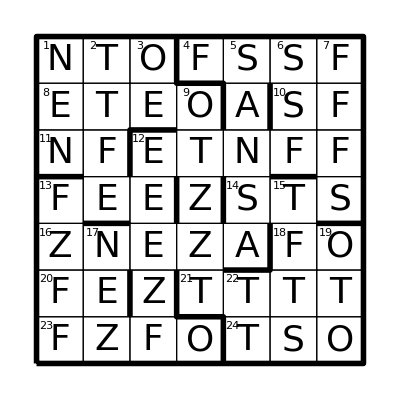

```mathematica
DisplaySolution[solution1]
```

```mathematica
Intersection[(clues/.rules1)/.{a_,b_}:>{a,IntegerDigits[b]/.german},solution1][[;;,1]]
```

{10,11,13,16,25,29,30}

```mathematica
(Select[clues,MemberQ[%28,First[#]]&]/.rules1)/.{a_,b_}:>{a,StringJoin@@(IntegerDigits[b]/.english)}
```

{{10,SF},{11,NF},{13,FOO},{16,TNOTE},{25,NON},{29,SENSE},{30,SSF}}

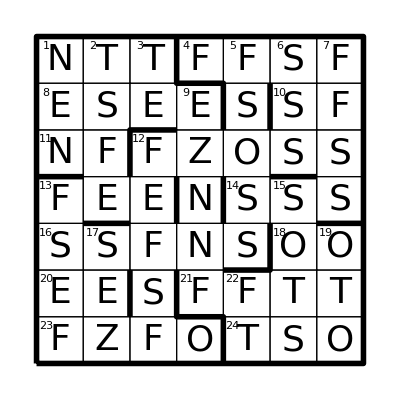

```mathematica
DisplaySolution[solution2]
```